## Kittipong Tapyou 65070501003

# Homework 02 : Thresholding

## Load Image

```mathematica
imgs = {-Graphics-, -Graphics-, -Graphics-
	, -Graphics-, -Graphics-, -Graphics-};
```

## Convert image to grayscale

```mathematica
ImgToGray[img_, weight_] := Module[{dim, grayData, imgData},
    dim = ImageDimensions[img];
    imgData = ImageData[img, "Byte"];
    grayData = Table[
             Dot[weight, imgData[[i, j, {1, 2, 3}]]],
             {i, dim[[2]]}, {j, dim[[1]]}];
    Return[grayData];
]
```

```mathematica
grayImgs = Table[ImgToGray[img, {0.3, 0.59, 0.11}], {img, imgs}];
```

```mathematica
GraphicsGrid[
	ArrayReshape[
		Table[
			Image[grayImg, "Byte"]
		,{grayImg, grayImgs}]
	, {2, 3}]
]
```

-Graphics-

## Plot histogram of gray intensity

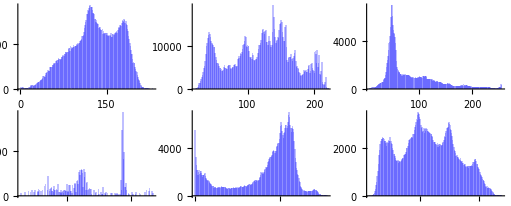

```mathematica
GraphicsGrid[
	ArrayReshape[
		Table[
			Histogram[Flatten[grayImg, 1], {1}, ChartStyle -> {Opacity[.25, Blue]}]
			, {grayImg, grayImgs}
		]
	, {2, 3}]
]
```

## Convert grayscale image to binary image

```mathematica
GrayToBin[img_, thres_] := Module[{dim},
	dim = Dimensions[img];
	Return[
		Table[If[img[[i, j]] > thres, 1, 0], {i, dim[[1]]}, {j, dim[[2]]}]
	];
]
```

```mathematica
threshold = {150, 130, 80, 120, 150, 130};
binImgs = Table[GrayToBin[grayImgs[[i]], threshold[[i]]], {i, Length[threshold]}];
```

```mathematica
GraphicsGrid[
	ArrayReshape[
		Table[
			Image[binImg]
		,{binImg, binImgs}]
	, {2, 3}]
]
```

-Graphics-